# Gap Statistic

```mathematica
Needs@"ErrorBarPlots`";
Needs@"HierarchicalClustering`";
```

```mathematica
withinClusterDistance[clusterList_List,distanceFunction_:SquaredEuclideanDistance](*Subscript[W, k]*):=(
allPossiblePairs=Subsets@@{clusterList,{2}};
setSize=Length@clusterList;
totalDistance=Total@((distanceFunction@@#)&/@allPossiblePairs);
Return@(totalDistance/2/setSize);
);

generateReferenceSets[dataset_List,B_Integer]:=(
transposedDataset=Transpose@dataset;
minsAndMaxes={Min@#,Max@#}&/@transposedDataset;
profileGenerator=Hold@RandomVariate@(UniformDistribution@#)&/@minsAndMaxes;
Return@(referenceSet=ReleaseHold@profileGenerator&/@Range[B]);
);

calculateGapStatistic[dataset_List,B_Integer,distanceFunction_:SquaredEuclideanDistance,upper_Integer:10]:=(
clusters=FindClusters@@{dataset,#,DistanceFunction->distanceFunction,Method->{"Agglomerate",Linkage->"Ward"}}&/@Range@upper;
Subscript[W, k]=Total/@(withinClusterDistance/@#&)/@clusters;

numberOfProfiles=Length@dataset;

referenceSets=Table[generateReferenceSets@@{dataset,numberOfProfiles},{i,1,B}];
clusteredReferenceSets=Function[referenceSet,FindClusters@@{referenceSet,#,DistanceFunction->distanceFunction,Method->{"Agglomerate",Linkage->"Ward"}}&/@Range@upper]/@referenceSets;
aaaaa=clusters;

Subscript[W, kb]=Function[referenceCluster,Total/@(withinClusterDistance/@#&)/@referenceCluster]/@clusteredReferenceSets;

Subscript[sd, k]=StandardDeviation@Log@Subscript[W, kb];
Subscript[s, k]=Subscript[sd, k] Sqrt@(1+1/B);

Return@{(Mean@Log@Subscript[W, kb]-Log@Subscript[W, k]),Subscript[s, k]};
);
```

# Gap on test data

```mathematica
CircleA=Table[{RandomVariate[NormalDistribution[0,1]],RandomVariate[NormalDistribution[0,1]]},{i,1,20}];
CircleB=Table[{RandomVariate[NormalDistribution[3,1]],RandomVariate[NormalDistribution[5,1]]},{i,1,20}];
CircleC=Table[{RandomVariate[NormalDistribution[5,1]],RandomVariate[NormalDistribution[0,1]]},{i,1,20}];
testData=Join[CircleA,CircleB,CircleC];
```

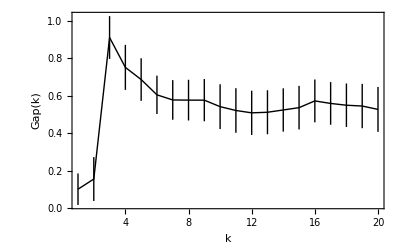

```mathematica
gapVector=calculateGapStatistic[testData,100,SquaredEuclideanDistance,20];
ErrorListPlot[Transpose@gapVector,
PlotRange->All,
Joined->True,
PlotStyle->{Thick,Black},
LabelStyle->Directive[FontFamily->"Futura",22],
Frame->True,
FrameLabel->{"k","Gap(k)"}
]
```